```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\mouze\Desktop\CM_labs\lab6\lab6

```mathematica
symm = Import["batchedSymm.txt","Table"];
explicit = Import["batchedEulerExplicit.txt", "Table"];
implicit =Import["ImplicitEuler.txt","Table"];
RK = Import["batchedRK.txt","Table"];
```

```mathematica
ListPlot[{explicit, implicit,symm,RK}, PlotRange->{{-5,5},{-5,5}},ImageSize->700,PlotLegends->{"Явный Эйлер","Неявный Эйлер", "Симметричная схема", "метод Рунге-Кутты 4 порядка"}]
```

-Graphics-

```mathematica
auto = Import["AutomatedStep.txt","Table"]
```

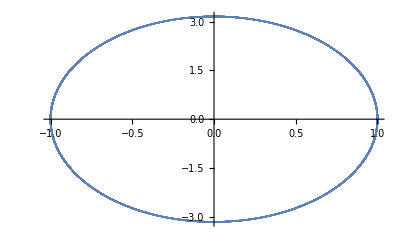

```mathematica
ListPlot[auto]
```

```mathematica
k= 10;
m = 1;
syst = {x'[t] == y, y'[t]==- k/m * x}
```

{x'[t]==y,y'[t]==-10 x}

```mathematica
DSolve[{syst, x[0] == 1, y[0] == 0},{x[t],y[t]}]
```

DSolve::argm: DSolve called with 2 arguments; 3 or more arguments are expected.

DSolve[{{x'[t]==y,y'[t]==-10 x},x[0]==1,y[0]==0},{x[t],y[t]}]